```mathematica
(* HFAG, Combined phiss, DGs including correlated statistical and systematical uncertainties 
   Rick van Kooten, Olivier Leroy, Summer 2014; use functions to cross check histogram combos *)
```

{-0.00851952,0.,0.0380255,0.0805,0.0091,0.0032,0.6603,0.0027,0.0015}

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{FontFamily→Helvetica,FontSize→18},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourLabels→Automatic,ContourLines→True,Contours→Automatic,ContourShading→Automatic,ContourStyle→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→{},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

-Graphics-

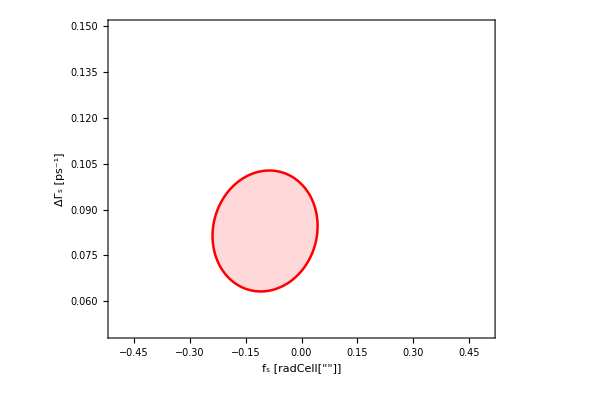

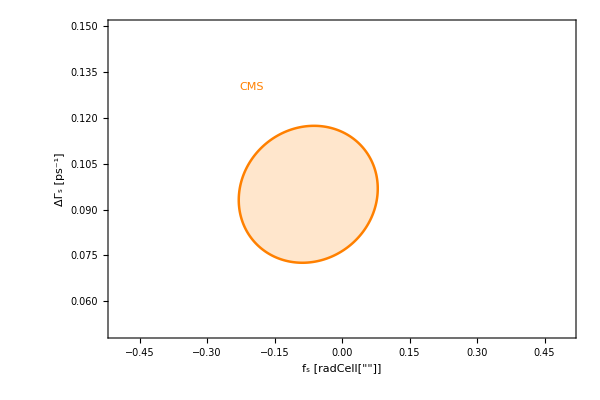

-Graphics-

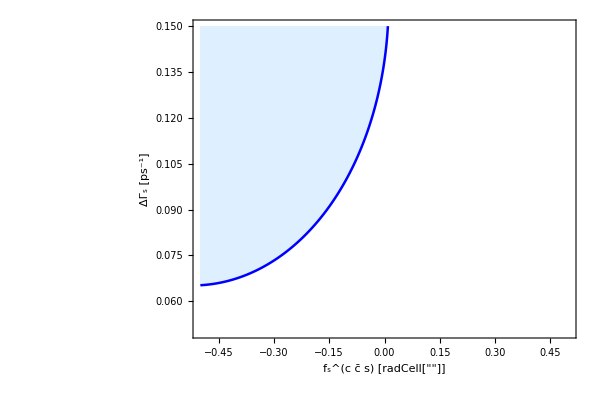

-Graphics-

-Graphics-

{xfit→-0.0296418,yfit→0.0838724,errxx→0.0327564,erryy→0.00653681,rho→0.0294178}

0.0294178

-Graphics-

OutputStream[results_phisDGs_Summer2016.txt,74]

results_phisDGs_Summer2016.txt

-Graphics-

-Graphics-

```mathematica
(* Clear individual and combined PDF functions *)
Clear[f, pdfJpsihh, pdfLHCb,pdfATLAS,pdfCMS,pdfCDF,pdfD0];

(* Plot ranges for phis and DGs - RvK: note that I "zoomed" in a bit more as precision increases *)
phismin = -0.5;
phismax = 0.5;
DGsmin = 0.05;
DGsmax = 0.15;


(* First give JpsiPhi results for LHCb,ATLAS, CMS, CDF and D0 *)

(* LHCb inputs ================================================================================ *)
(* Official JpsiKK+JpsiPiPi 3fb-1 LHCb combination + DsDs*)


myinput=ReadList["inputsHFAG_Summer2016.txt",Number]
phisLHCb = myinput[[1]];
phisLHCbestat = myinput[[2]];
phisLHCbesyst = myinput[[3]];
phisLHCbetot = Sqrt[phisLHCbestat^2+phisLHCbesyst^2]; (* error tot *) 


(*for DGs LHCb, only uses JpsiKK 3fb-1, since JpsiPiPi3fb-1 is not yet available*)

DGsLHCb = myinput[[4]];
DGsLHCbestat =  myinput[[5]];
DGsLHCbesyst = myinput[[6]];

DGsLHCbetot = Sqrt[DGsLHCbestat^2+DGsLHCbesyst^2]; (* = 0.0096462*)
(*Use combined DGs LHCb value instead of the JpsiKK alone
DGsLHCb = 0.0873; 
DGsLHCbestat = 999.;
DGsLHCbesyst = 999.;
DGsLHCbetot = 0.0080; *)

rhostaLHCb=0.; (* stat correl between Gs and DGs *)
rhosysLHCb = 0.; (* assume no correlated systematics between Gs and DGs *)
rhoLHCb = 0.0; (* correl tot including stat and syst*)

(* LHCb psi2S inputs =================================================================== *)

phisLHCbPsi2S = +0.23;
phisLHCbPsi2Sestat =0.285;
phisLHCbPsi2Sesyst = 0.02;
phisLHCbPsi2Setot = Sqrt[phisLHCbPsi2Sestat^2+phisLHCbPsi2Sesyst^2];

DGsLHCbPsi2S = 0.066;
DGsLHCbPsi2Sestat =  0.0425;
DGsLHCbPsi2Sesyst = 0.006;
DGsLHCbPsi2Setot = Sqrt[DGsLHCbPsi2Sestat^2+DGsLHCbPsi2Sesyst^2];

rhostaLHCbPsi2S=0.19; 
rhosysLHCbPsi2S = 0.;(* assume no correlated systematics between phis and DGs *)
rhoLHCbPsi2S = (phisLHCbPsi2Sestat*DGsLHCbPsi2Sestat*rhostaLHCbPsi2S+phisLHCbPsi2Sesyst*DGsLHCbPsi2Sesyst*rhosysLHCbPsi2S)/(phisLHCbPsi2Setot*DGsLHCbPsi2Setot); 

(* ATLAS inputs ================================================================================ *)
(* taking this from altas run1 published paper *)
phisATLAS = -0.098;
phisATLASestat =0.084;
phisATLASesyst = 0.040;
phisATLASetot = Sqrt[phisATLASestat^2+phisATLASesyst^2];

DGsATLAS = 0.083;
DGsATLASestat =  0.011;
DGsATLASesyst = 0.007;
DGsATLASetot = Sqrt[DGsATLASestat^2+DGsATLASesyst^2];

rhostaATLAS=0.107; 
rhosysATLAS = 0.;(* assume no correlated systematics between phiss and DGs *)
rhoATLAS = (phisATLASestat*DGsATLASestat*rhostaATLAS+phisATLASesyst*DGsATLASesyst*rhosysATLAS)/(phisATLASetot*DGsATLASetot); (* =.08623667; *)


(* CMS inputs ================================================================================ *)
(* Private Email Jack, 15 july 2015, for EPS 20fb-1 8TeV result only*)
phisCMS = -0.075;
phisCMSestat  = 0.097;
phisCMSesyst = 0.031;
phisCMSetot = Sqrt[phisCMSestat^2+phisCMSesyst^2];

DGsCMS = 0.095;
DGsCMSestat =  0.013;
DGsCMSesyst = 0.007;
DGsCMSetot = Sqrt[DGsCMSestat^2+DGsCMSesyst^2];

rhostaCMS=0.10; 
rhosysCMS =0.;(* assume no correlated systematics between Gs and DGs *)
rhoCMS = (phisCMSestat*DGsCMSestat*rhostaCMS+phisCMSesyst*DGsCMSesyst*rhosysCMS)/(phisCMSetot*DGsCMSetot); 


(* CDF inputs ================================================================================ *)
(* Taken from Phys.Rev.Lett 109,171802 (2012), assuming phis Gaussian and centered *)
phisCDF =-0.24;
phisCDFestat =999.;
phisCDFesyst =999.;
phisCDFetot = 0.36;

DGsCDF = 0.068;
DGsCDFestat =  0.026;
DGsCDFesyst = 0.009;
DGsCDFetot = Sqrt[DGsCDFestat^2+DGsCDFesyst^2];

rhostaCDF=999.; (* -0.5 stat only *)
rhosysCDF = 999.;(* assume no correlated systematics between Gs and DGs *)
rhoCDF = 0.0; (* Assuming from their Fig. 2 *)

(* D0 inputs ================================================================================ *)
(* Taken from Phys Rev D 85, 032006 (2011) *)
phisD0 =-0.55;
phisD0estat = 999.;
phisD0esyst =999.;
phisD0etot = 0.37; (* symmetrize this uncertainty *)

DGsD0 = 0.163;
DGsD0estat =  0.0645;
DGsD0esyst = 0.0;
DGsD0etot = Sqrt[DGsD0estat^2+DGsD0esyst^2];

rhostaD0=-0.05; (* RickVK: http://www-d0.fnal.gov/Run2Physics/WWW/results/final/B/B11C/ *)
rhosysD0 =0;(* assume no correlated systematics between phis and DGs *)
rhoD0 = -0.05; (* correl tot including stat and syst*)


(* Now start the combination ============================================================= *)

(* Joint pdf of Gs and DGs for JpsiPhi-like channels *)
f[x_,y_,phis_,ephis_,DGs_,eDGs_,rho_]:=1/(2*Pi*ephis*eDGs*Sqrt[1-rho^2])*Exp[(-1./(2*(1-rho^2)))*((x-phis)^2/ephis^2 + (y-DGs)^2/eDGs^2- 2*rho*(x-phis)*(y-DGs)/(ephis*eDGs))];


pdfJpsihh[x_,y_]:=f[x,y,phisLHCb,phisLHCbetot,DGsLHCb,DGsLHCbetot,rhoLHCb]*f[x,y,phisLHCbPsi2S,phisLHCbPsi2Setot,DGsLHCbPsi2S,DGsLHCbPsi2Setot,rhoLHCbPsi2S]*f[x,y,phisATLAS,phisATLASetot,DGsATLAS,DGsATLASetot,rhoATLAS]*
f[x,y,phisCMS, phisCMSetot, DGsCMS, DGsCMSetot, rhoCMS]*
f[x,y,phisCDF,phisCDFetot,DGsCDF,DGsCDFetot,rhoCDF]*
f[x,y,phisD0,phisD0etot,DGsD0,DGsD0etot,rhoD0];

pdfLHCb[x_,y_] := f[x,y,phisLHCb,phisLHCbetot,DGsLHCb,DGsLHCbetot,rhoLHCb]*f[x,y,phisLHCbPsi2S,phisLHCbPsi2Setot,DGsLHCbPsi2S,DGsLHCbPsi2Setot,rhoLHCbPsi2S];
pdfATLAS[x_,y_] := f[x,y,phisATLAS,phisATLASetot,DGsATLAS,DGsATLASetot,rhoATLAS];
pdfCMS[x_,y_] := f[x,y,phisCMS, phisCMSetot, DGsCMS, DGsCMSetot, rhoCMS];
pdfCDF[x_,y_] := f[x,y,phisCDF,phisCDFetot,DGsCDF,DGsCDFetot,rhoCDF];
pdfD0[x_,y_]:= f[x,y,phisD0,phisD0etot,DGsD0,DGsD0etot,rhoD0];

(* Default font options on the contour plots *)
SetOptions[ContourPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->18}]


(* Individual inputs, use Delta(log(L))=1.15 for plotting of 68% CL regions *)
minLHCb =FindMinValue[ -1*pdfLHCb[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contourLHCb=-1.0*minLHCb*Exp[-1.15];
plotLHCb = ContourPlot[pdfLHCb[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},Contours->{contourLHCb},ContourStyle->{RGBColor[0.13,0.55,0.13],Thickness[0.003]},PlotPoints->150,PlotRange->Full, ContourShading->{Transparent,Green},Axes->True, FrameLabel->{Style["f_s^(c c̄ s) [radCell[""]]",Black,24],Style["ΔΓ_s [ps^-1]",Black,24]},ImageSize->{600,400},AspectRatio->Full,AxesOrigin->{-1.5,0},Epilog->{Text[Style["LHCb",Large, RGBColor[0.14,0.55,0.13]],{0.35,0.127}]}] 

minATLAS =FindMinValue[ -1*pdfATLAS[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contourATLAS=-1.0*minATLAS*Exp[-1.15];
plotATLAS = ContourPlot[pdfATLAS[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},Contours->{contourATLAS},ContourStyle->{Red,Thickness[0.003]},PlotPoints->150,PlotRange->Full, ContourShading->{Transparent,LightRed},Axes->True, FrameLabel->{Style["f_s [radCell[""]]",Bold,Black],Style["ΔΓ_s [ps^-1]",Bold,Black]},ImageSize->{600,400},AspectRatio->Full,AxesOrigin->{-1.5,0},Epilog->Text[Style["ATLAS",Large, Red],{0.7,0.035}]] 

minCMS =FindMinValue[ -1*pdfCMS[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contourCMS=-1.0*minCMS*Exp[-1.15];
plotCMS = ContourPlot[pdfCMS[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},Contours->{contourCMS},ContourStyle->{Orange,Thickness[0.003]},PlotPoints->150,PlotRange->Full, ContourShading->{Transparent,LightOrange, Opacity[0.5]},Axes->True, FrameLabel->{Style["f_s [radCell[""]]",Bold,Black],Style["ΔΓ_s [ps^-1]",Bold,Black]},ImageSize->{600,400},AspectRatio->Full,AxesOrigin->{-1.5,0},Epilog->{Text[Style["CMS",Large, Orange],{-0.2,0.130}]}] 

minCDF =FindMinValue[ -1*pdfCDF[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contourCDF=-1.0*minCDF*Exp[-1.15];
plotCDF = ContourPlot[pdfCDF[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},Contours->{contourCDF},ContourStyle->{Magenta,Thickness[0.003]},PlotPoints->150,PlotRange->Full, ContourShading->{Transparent,LightMagenta},Axes->True, FrameLabel->{Style["f_s [radCell[""]]",Bold,Black],Style["ΔΓ_s [ps^-1]",Bold,Black]},ImageSize->{600,400},AspectRatio->Full,AxesOrigin->{-1.5,0},Epilog->{Text[Style["CDF",Large, Magenta],{-0.89,0.039}]}] 

minD0 =FindMinValue[ -1*pdfD0[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contourD0=-1.0*minD0*Exp[-1.15];
plotD0 = ContourPlot[pdfD0[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},Contours->{contourD0},ContourStyle->{Blue,Thickness[0.003]},PlotPoints->150,PlotRange->Full, ContourShading->{Transparent,LightBlue},Axes->True, FrameLabel->{Style["f_s^(c c̄ s) [radCell[""]]",Bold,Black],Style["ΔΓ_s [ps^-1]",Bold,Black]},ImageSize->{600,400},AspectRatio->Full,AxesOrigin->{-1.5,0},Epilog->Text[Style["DØ",Large, Blue],{-0.9,0.14}]] 

(* Combined *)
mintot =FindMinValue[ -1*pdfJpsihh[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contourtot=-1.0*mintot*Exp[-1.15];
plottot = ContourPlot[pdfJpsihh[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},Contours->{contourtot},ContourStyle->{Gray,Thickness[0.005]},PlotPoints->150,PlotRange->Full, ContourShading->{Transparent,LightGray},Axes->True, FrameLabel->{Style["f_s^(c c̄ s) [radCell[""]]",Black,24],Style["ΔΓ_s [ps^-1]",Black,24]},ImageSize->{600,400},AspectRatio->Full,AxesOrigin->{-1.5,0}] 

(* Combined, use this particular contour of Delta(log(L)) = 0.5 to find the errors (i.e., full extent of ellipse *)
min1 =FindMinValue[ -1*pdfJpsihh[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contour1=-1.0*min1*Exp[-0.5];
myplot1 = ContourPlot[pdfJpsihh[x,y],{x,phismin, phismax},{y,DGsmin,DGsmax},Contours->{contour1},PlotPoints->150,PlotRange->Full, ContourShading->{White,LightGray},Axes->True, FrameLabel->{Style["f_s [radCell[""]]",Bold,Black,],Style["ΔΓ_s [ps^-1]",Bold,Black]},ImageSize->{600,400},AspectRatio->Full] 

(* This code grabs the points of the contour of Delta(log(L)) = 0.5 and finds the minimum and maximum extent in each *)
(* dimension of the ellipse to find the 1D 1-sigma errors by finding the difference to the minimum *)
xmin =x/.Last[FindMinimum[-1*pdfJpsihh[x,y],{x,phismin,phismax},{y,DGsmin,DGsmax},MaxIterations->100]];
ymin = y/.Last[FindMinimum[-1*pdfJpsihh[x,y],{x,phismin,phismax},{y,DGsmin,DGsmax},MaxIterations->100]]; 

(* Finds asymmetric uncertainties *)
points=Cases[Normal@myplot1,x_Line:>First@x,Infinity];
eplusphis=Max[points[[1]][[All,1]]]-xmin;
eminusphis = xmin-Min[points[[1]][[All,1]]];
eplusDGs = Max[points[[1]][[All,2]]]-ymin;
eminusDGs = ymin-Min[points[[1]][[All,2]]];

(* However, to find correlations, symmetrize the uncertainties *)
errphis=(eplusphis+eminusphis)/2;
errDGs=(eplusDGs+eminusDGs)/2;

(* Find correlation *)
(* by getting list of (x,y) coordinates and fitting an ellipse with correlation to them *)

list2=First[points];
(*how many (x,y) points*)
veclen=Length[list2];
(*make a vector same length,filled with value of 1.0*)

vecones=Table[1.0,{i,veclen}];
(*effectively insert to each pair of (x,y) points,i.e.,(x,y,1.0),desired value of expression at (x,y)*)

fitlist=Transpose[Append[Transpose[list2],vecones]];
(*tilted error ellipse*)

ellipse=(xx-xfit)^2/errxx^2-2*rho*(xx-xfit)*(yy-yfit)/(errxx*erryy)+(yy-yfit)^2/erryy^2+rho^2;
(*fit to (x,y) points;use starting values determined above*)
fit=FindFit[fitlist,ellipse,{{xfit,xmin},{yfit,ymin},{errxx,errphis},{erryy,errDGs},{rho,0}},{xx,yy}]
rhocor=rho/.Last[fit]
ListPlot[points,PlotRange->{{phismin,phismax},{DGsmin,DGsmax}}]

(* Output fit results into text file *)
str=OpenWrite["results_phisDGs_Summer2016.txt"]
WriteString[str,"Result from the global fit : \n =========================================================================== \n"]
WriteString[str,"DGs = ", ymin, "^{+", eplusDGs , "} _{-", eminusDGs,"} \n"]
WriteString[str,"phis = ", xmin, "^{+", eplusphis , "} _{-", eminusphis,"} \n"]
WriteString[str,"rho(phis,DGs) = ",rhocor ,"\n"]

Close[str]

(* All overlaid: DGs vs. phis *)
finalPloterr = Show[myplot1]
(* Go grab the logo graphic file *)
g=Import["http://marwww.in2p3.fr/~oleroy/pro/hfag/Summer2016/hfag_logo_Summer2016.pdf"];
logo=Show[g];
(* Final plot fully annotated *)(*finalPlot = Show[plottot,plotLHCb,plotATLAS,plotCMS,plotCDF,plotD0,logo,ImageSize->{600,400},AspectRatio->Full,Epilog->{ *)

(*finalPlot = Show[plotD0, plotCDF, plotATLAS,plotCMS,plotLHCb,plottot,ImageSize->{600,400},*)
(*Text[Style["Preliminary",17],{0.3,0.125}],*)
finalPlot = Show[plotD0, plotCDF, plotCMS,plotATLAS,plotLHCb,plottot,ImageSize->{600,400},AspectRatio->Full,Epilog->{
Text[Style["68% CL regions",17],{0.3,0.12}],
Text[Style[ToExpression["( \\Delta\\log{\\cal{L}= 1.15 )}",TeXForm,HoldForm],17],{0.3,0.115}],
Text[Style["LHCb 3fb^-1",18, RGBColor[0.14,0.55,0.13]],{0.1,0.1}],
Text[Style["ATLAS 19.2fb^-1",18, Red],{-0.35,0.063}],
Text[Style["CMS 19.7fb^-1",18, Orange],{0.,0.125}],
Text[Style["CDF 9.6fb^-1",18, Magenta],{-0.4,0.10}],
Text[Style["DØ 8fb^-1",18, Blue],{-0.1,0.145}],
Text[Style["Combined",18,Black],{0.08,0.08}],
Text[Style["SM",18,Black],{-0.0363,0.063}],
Inset[Graphics[Rectangle[{0.0,0.0},{0.04,1}]],{-0.03764,0.088},{Center,Center},{0.039,0.040}],
Inset[Show[g],{0.4,0.14}]
}]
(*phis^SM from CKMfitter2015 *)
(* sigma phis SM =  scale of triangle (2*0.00078)/0.04=0.039 (no peng) 
  sigma(DGs)= 0.020  *2 = 0.040 DGs from Artuso,Borrisov,Lenz, *http: //arxiv.org/abs/1511.09466 *)

(*Inset[Show[g],{1.3,0.185}], *)
(* Save in all reasonable formats - pick and choose *)
Export["DGsVersusphis_Summer2016_Zoom.pdf",finalPlot];
Export["DGsVersusphis_Summer2016_Zoom.jpg",finalPlot];
Export["DGsVersusphis_Summer2016_Zoom.eps",finalPlot];
```